# Performance on Trotter vs recompilation

Note: Use mathematica 12, mathematica 13 is buggy in the pattern part

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"];
```

```mathematica
Import["https://qtechtheory.org/questlink.m"];
SetDirectory[NotebookDirectory[]];
CreateLocalQuESTEnv["quest_link_cpu"];
```

## Modules

### Distance-related modules

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_,total_:False]:=Module[{stringham,ham,nterms,nqubits},
stringham=Import[filename];
ham=ToExpression[stringham]/.{{a_?NumberQ}:>{a Subscript[Id, 0]}};
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
If[total,
{Total@Apply[Times,ham,1],nterms,nqubits}
,
{ham,nterms,nqubits}
]
]

GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]

CountGates::usage="CountGates[circuit], return the count for {cnots, singles}";
CountGates[circuit_]:=Module[{cnotc},
cnotc=Count[circuit/.{Subscript[C, _][_]->2,Subscript[_, _]-> 1,Subscript[_, _][_]->1},2];
{cnotc,Length@circuit-cnotc}
]

SetAttributes[MergeGates,HoldFirst]
MergeGates::usage="MergeGates[circuits], simplify circuits.";
MergeGates[circuits_]:=Module[{circc,circs,len,a,b,c,d,e,f,θ,j,i},
circs=Flatten@circuits;
While[True,
len=Length@circs;
circc=GetCircuitColumns[circuits];
circc=circc//.{
{a___,{b___,Subscript[H, j_],c___},{d___,Subscript[H, j_],e___},f___}:>{a,{b,c},{d,e},f},
{a___,{b___,Subscript[Rx, j_][θ_],c___},{d___,Subscript[Rx, j_][-θ_],e___},f___}:>{a,{b,c},{d,e},f},
{a___,{b___,Subscript[Rx, j_][-θ_],c___},{d___,Subscript[Rx, j_][θ],e___},f___}:>{a,{b,c},{d,e},f},
{a___,{b___,Subscript[Rx, j_][θ_],c___},{d___,Subscript[Rx, j_][θ_],e___},f___}:>{a,{b,Subscript[Rx, j][2θ],c},{d,e},f},
{a___,{b___,Subscript[C, j_][Subscript[X, i_]],c___},{d___,Subscript[C, j_][Subscript[X, i_]],e___},f___}:>{a,{b,c},{d,e},f}
};
circs=Flatten@circc;
If[Length@circs===len,
Break[]]
];
circs
]

MatrixDist::usage="MatrixDist[matrix1, matrix2, subspace, plotglobalphase:False]. Calculate distance of 2 matrices by formula: 
                                    max_λ |Π_S(U-V)Π_S| 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,subspace_,plotglobalphase_:False]:=Module[{sm1,sm2,globalphase,mindist,F,ϕ},
{sm1,sm2}=If[Length@subspace<Length@M1,{GetSubMatrix[M1,subspace],GetSubMatrix[M2,subspace]},{M1,M2}];
F[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->6,MaxIterations->2000,Method->"RandomSearch"];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"},PlotLabel->ToString@subspace]];
{mindist,ϕ/.globalphase}
]


distMatrices::usage="distMatrices[M1,M2,subspace], return <|fullopt->dfullopt,subopt->dsubopt,fullsubopt->dfullsubopt|> "
distMatrices[M1_,M2_,subspace_]:=Module[{globalphase,mindist,fullopt,subopt,fullsubopt,dsubopt,dfullopt,dfullsubopt,ϕ,dynmat},
subopt[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
fullopt[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]];
fullsubopt[ϕ_?NumericQ]:=Max[Re[Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]][[1+subspace]]];
{dfullopt,globalphase}=NMinimize[{fullopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->2000,Method->"RandomSearch"];
If[Length@subspace<Length@M1,
{dsubopt,globalphase}=NMinimize[{subopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->2000,Method->"RandomSearch"];
{dfullsubopt,globalphase}=NMinimize[{fullsubopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->2000,Method->"RandomSearch"];
,
{dfullsubopt,globalphase}={dfullopt,globalphase};
{dsubopt,globalphase}={dfullopt,globalphase}
];
<|"fullopt"->dfullopt,"subopt"->dsubopt,"fullsubopt"->dfullsubopt|>
]



GetSubMatrix::usage="GetSubMatrix[matrix,subspace]. Return the submatrix in the subspace.";
GetSubMatrix[matrix_,subspace_ ]:=Module[{sm,dim,x=0,y=0},
dim=Length@subspace; 
sm=IdentityMatrix[dim];
Table[
++x;y=0;
Table[
++y;
sm⟦x,y⟧=matrix⟦s+1,ss+1⟧;
,{ss,subspace}]
,{s,subspace}];
sm
]
```

distMatrices[M1,M2,subspace], return <|fullopt->dfullopt,subopt->dsubopt,fullsubopt->dfullsubopt|>

### Trotterization-related modules

Reference:
https://aip.scitation.org/doi/10.1063/1.4768229

```mathematica
PauliCirc::usage="PauliCirc[coefficient, pauli_list, nqubits, prefactor]. Return the circuit of a term.";
PauliCirc[coef_,paulis_,nqubits_,factor_:1]:=Module[{circ,p,q,ngates},
If[Length@paulis>0,
circ=Table[
{p,q}=Level[c,-1];
Which[p===Z,{Subscript[C, q][Subscript[X, nqubits]]},p===X,{Subscript[Ry, q][π/2],Subscript[C, q][Subscript[X, nqubits]],Subscript[Ry, q][-π/2]},p===Y,{Subscript[Rx, q][-π/2],Subscript[C, q][Subscript[X, nqubits]],Subscript[Rx, q][π/2]}]
,{c,paulis}];
Join[circ,{{Subscript[Rz, nqubits][coef*factor]}},Reverse@circ]
,
circ={}
]
]


Propagator::usage="Propagator[coefficient, pauli_list, nqubits, prefactor]. Return the circuit of a propagator.";
Propagator[coef_,paulis_,factor_]:=Module[{lpaulis,p,q,ngates,ops,ids,rops,ropsd,rcnot,j,i,pauliops},
rops={Subscript[X, j_]:>Subscript[H, j], Subscript[Y, j_]:>Subscript[Rx, j][-π/2], Subscript[Z, _]:>{}};
ropsd={Subscript[X, j_]:>Subscript[H, j], Subscript[Y, j_]:>Subscript[Rx, j][π/2], Subscript[Z, _]:>{}};
rcnot={{i_Integer,j_Integer}:>Subscript[C, i][Subscript[X, j]] ,{{_Integer}}:>{} };
lpaulis=Table[{p,q}=Level[c,-1],{c,paulis}];
lpaulis=SortBy[lpaulis,#⟦2⟧&];
{ops,ids}={lpaulis⟦All,1⟧,Partition[lpaulis⟦All,2⟧,2,1]};
If[Length@ids<1, ids={lpaulis⟦All,2⟧}];
pauliops=Subscript[#⟦1⟧, #⟦2⟧]&/@lpaulis;
Flatten@{pauliops/.rops,ids/.rcnot,Subscript[Rz, Last@Last@ids][2*coef*factor],Reverse[ids/.rcnot],pauliops/.ropsd}
]


IsCommute::usage="IsCommute[List_paulis1, List_paulis2]. Return boolean indicates commutativity.";
IsCommute[P1_List,P2_List]:=Module[{m1,m2,nq,i},
nq=1+Max[Flatten@{P1,P2}/.Subscript[_, i_]->i];
m1=CalcCircuitMatrix[P1,nq];
m2=CalcCircuitMatrix[P2,nq];
If[Norm[m1.m2-m2.m1]≤10^-13,
True,
False]
]

PartitionPaulis::usage="ParititionPaulis[paulis], partition a list of pauli operators by commutation.";
PartitionPaulis[paulis_List]:=Module[{list1, list2},
list1={paulis⟦1⟧};list2={};
Table[
If[(AllTrue@@IsCommute[p⟦2;;⟧,#⟦2;;⟧]&/@list1)⟦1⟧,
AppendTo[list1,p],AppendTo[list2,p]]
,{p,paulis⟦2;;⟧}];
(*sanity checck*)
If[¬AllTrue[IsCommute[#⟦1⟧⟦2;;⟧,#⟦2⟧⟦2;;⟧]&/@Subsets[list1,{2}]],
Print["ERR: there is a non-commuting operation in set A"]];
If[¬AllTrue[IsCommute[#⟦1⟧⟦2;;⟧,#⟦2⟧⟦2;;⟧]&/@Subsets[list2,{2}]],
Print["ERR: there is a non-commuting operation in set B"]];
{list1,list2}
]

TrotterizeNaive::usage="TrotterizeNaive[hamiltonian_path, t, n]. Return the trotterization circuit, if full=False, it's not powered by n yet.";
TrotterizeNaive[hamfile_,t_,n_]:=Module[{ham,nqubits,nterms,r=N[t/n],estgates,esterr,circ},
{ham,nterms,nqubits}=FormatHamiltonian[hamfile,False];
ham=DeleteCases[ham,{_}]; (*delete the global phase*)
estgates=(2*Length@Flatten@ham-nterms)*n;
esterr=r^2//N;
circ=Flatten[Table[Propagator[paulis⟦1⟧,paulis⟦2;;⟧,r],{paulis,ham}],1];
Flatten@ConstantArray[circ,n]
]


Trotterize::usage="Trotterize[hamiltonian_path, t, n, order:1]. Return the trotterization circuit. Available up to the fourth order.
The paulis are partitioned into two sets A and B in which each element is commuting each other. 
Trotterization is available up to the 4th order
order 1: e^((A + B) t)=(e^(At/n)e^(Bt/n))^n+O(t Δt)
order 2: e^((A + B) t)=(e^(At/2  n)e^(Bt/n)e^(At/2  n))^n+O(t Δt^2)
order 2comp: is order 2 but compressed
order 2scb :(e^(At/2  n)e^(Bt/n)e^(At/2  n))(e^(Bt/2  n)e^(At/n)e^(Bt/2  n))(e^(At/2  n)e^(Bt/n)e^(At/2  n))
order 3: e^((A + B) t)=(e^(7/24)e^(2/3)e^(3/4)e^(-2/3)e^(-1/24)e^(Bt/n))^n+O(t Δt^3)
order 4: e^((A + B) t)=Π_(i = 1,  ... , 5)(e^p_ie^p_ie^p_i)^n+O(t Δt^4),where p1=p2=p4=p5=1/(4-4^(1/3)),p3=1-4p1
";
Trotterize[hamfile_,t_,n_,order_:1]:=Module[{ham,nterms,nqubits,list1,list2,Δt,f},
{ham,nterms,nqubits}=FormatHamiltonian[hamfile,False];
ham=DeleteCases[ham,{_}]; (*delete the global phase*)
{list1,list2}=PartitionPaulis[ham];
Which[
order===1,
f=N[t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]
},{n}]
,
order===2,
f=N[0.5*t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]
},{n}]
,
(*compressed2 -- check if it results in the circuit order 2
template: Flatten@{e^(A/2),e^B,Table[{e^A,e^B},{n-1}],e^(A/2)}
*)
order ==="2comp",
f=N[0.5*t/n];
Flatten@{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[{Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list1}],Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}]},{n-1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]
}
,
(*simon's version of order 2*)
order==="2scb",
f=N[0.5*t/n];
Flatten@Table[
If[OddQ@iter,
{Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]}
,
{Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]}]
,{iter,n}] 
,
order===3,
f=N[t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(7/24)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(2/3)f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(3/4)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,((-2)/3)f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,((-1)/24)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]
},{n}]
,
order===4,
f=ConstantArray[N[1/(4-4^(1/3))],5];
f⟦3⟧=N[1-4f⟦1⟧];
f=(0.5*t/n)*f;
Flatten@Table[
Flatten[Flatten@{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,#],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2#],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,#],{p,list1}]
}&/@f]
,{n}]
]
]
```

### Plots, summary modules

```mathematica
getSummary::usage="getSummary[circuit, hamiltonianMatrix, t, observedState(ground state)].
Returns {{twos-count,singles-count}, distance, ent fidelity, <e-e'>, 1-<ψ(t)|ψ'(t)>}"
getSummary[circ_,hammat_,t_,state_,subspace_:Null]:=Module[{dham,approxmat,singles,twos,dist,nqubits,space,nancilla,nconst,sbasis,entstate,entfid,eerr,fiderr,vec,vecapprox},
(*analytic matrix as reference *)
nqubits=Log2@Length@hammat;
dham=MatrixExp[-ⅈ t hammat]//Chop;
approxmat=Block[{$IterationLimit=10000},CalcCircuitMatrix[circ,nqubits]];
space=If[subspace===Null,Range[0,2^nqubits-1],subspace];
(*gates count*)
{twos,singles}=CountGates[circ];
(*distance*)
dist=MatrixDist[dham,approxmat,space];
(*entanglement infidelity*)
nconst=N[1/(√Length[space])];  
nancilla=Max[Ceiling[Log2[Length@space]],1];
sbasis=Table[space⟦idx+1⟧+2^nqubits*idx,{idx,0,Length@space-1}];
entstate=ConstantArray[0.,2^(nqubits+nancilla)];
Table[entstate⟦k+1⟧=nconst,{k,sbasis}];
entfid=1-Abs[entstate.KroneckerProduct[Inverse[approxmat].dham,IdentityMatrix[2^nancilla]].entstate]^2;
(*expected energy*)
vec=dham.state;
vecapprox=approxmat.state;
eerr=Conjugate[vecapprox].hammat.vecapprox-Conjugate[vec].hammat.vec;
(*infidelity to the true evolution state*)
fiderr=1-Abs[Conjugate[vec].vecapprox]^2;
{{twos,singles},First@dist,entfid,Re@eerr,fiderr}
]
```

getSummary[circuit, hamiltonianMatrix, t, observedState(ground state)].
Returns {{twos-count,singles-count}, distance, ent fidelity, <e-e'>, 1-<ψ(t)|ψ'(t)>}

```mathematica
ClearAll[PlotEErr]
PlotEErr[trotsum_,label_,opts_:{}]:=Module[{eerr,minval,n,idxdata},
n=Length@Keys@trotsum;
eerr=If[label===1,
Table[Table[Labeled[{i,trotsum[order][[i,4]]},Total@trotsum[order][[i,label]],Right],{i,Length@trotsum[1]}],{order,Keys@trotsum}],
Table[Table[Labeled[{i,trotsum[order][[i,4]]},NumberForm[trotsum[order][[i,label]],2],Top,FrameMargins->None,FrameStyle->Transparent,Spacings->{0, 0}],{i,Length@trotsum[1]}],{order,Keys@trotsum}]
];
minval=Min[(Join@@Values[trotsum])[[All,4]]];
ListLogPlot[eerr,LabelStyle->{FontFamily->"Asana Math",FontSize->15,Background->None},FrameLabel->{"Trotter number",TraditionalForm["ΔE"]},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotStyle->PointSize[Medium],PlotRange->{{0.5,2+n},{10^Floor[Log10@minval],1}},Background->White,GridLines->{None, {chemacc}},GridLinesStyle->Directive[Red, Dashed,Thick],PlotLegends->Placed[PointLegend[Automatic,( "order "<>ToString[#]&/@Range[4]),Spacings->0.1,LegendMarkerSize->5,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False)]&)],
{0.9,0.9}],opts]
]

PlotDists[trotsum_,opts_:{}]:=Module[{dists},
dists={#[[2]],#[[4]]}&/@(Join@@Values@trotsum);
ListLogLinearPlot[dists,LabelStyle->{FontFamily->"Serif",FontSize->10,Background->None},FrameLabel->{"matrix distance","ϵ_energy"},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotStyle->PointSize[Medium],PlotRange->Automatic,Background->White,GridLines->{None, {chemacc}},GridLinesStyle->Directive[Red, Dashed,Thick],opts]
]
```

## H_2 molecule

### Plots on Trotterizations

```mathematica
filepath="~/vqe/molecules/H2/H2.txt";
{ham,nterms,nqubits}=FormatHamiltonian[filepath,True];
(*delete the global phase*)
hammat=CalcPauliSumMatrix[DeleteCases[ham,{_}]];
eigsys=Eigensystem[hammat];
(*groundstate vector*)
gsvec=First@eigsys[[2,Ordering[eigsys[[1]],1] ]];

chemacc=1.59*10^-3;
```

```mathematica
times={0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.1,0.15,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.9,1,1.1,1.2,1.35,1.5,1.65,1.8,2,2.2,2.35,2.55,2.85,3,3.3,3.5,3.7,4,4.3,4.5}
```

{0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.1,0.15,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.9,1,1.1,1.2,1.35,1.5,1.65,1.8,2,2.2,2.35,2.55,2.85,3,3.3,3.5,3.7,4,4.3,4.5}

```mathematica
trotsum<<trotsum.mx;
trotsumsub<<trotsumsub.mx;
```

#### Full/sub space distance on trotter calculation

```mathematica
filepath
```

~/vqe/molecules/H2/H2.txt

```mathematica
ClearAll[trotterSummary]
trotterSummary::usage="trotterSummary[hammat_,filepath_,t_,n_,order_,subspace_:Null].
Returns distances to the actual unitary and gate counts"
trotterSummary[hammat_,filepath_,t_,n_,order_,subspace_:Null]:=Module[{trotcirc,dham,approxmat,singles,twos,dists,nqubits},

(*analytic matrix as reference *)
nqubits=Log2@Length@hammat;
dham=MatrixExp[-ⅈ t hammat]//Chop;

(* trotter circuit*)
trotcirc=MergeGates[Trotterize[filepath, t, n, order]];
approxmat=Chop@Block[{$IterationLimit=10000},CalcCircuitMatrix[trotcirc,nqubits]];

(*gates count*)
{twos,singles}=CountGates[trotcirc];
(*distance*)
dists=distMatrices[dham,approxmat,subspace];
<|"ngates"->twos+singles,"dists"->dists|>
]
```

trotterSummary[hammat_,filepath_,t_,n_,order_,subspace_:Null].
Returns distances to the actual unitary and gate counts

```mathematica
subspace={3,5,6,9,10,12};
fullspace=Range[0,2^nqubits-1];
orders={1,"2scb",3,4};
maxn=<|1->56,"2scb"->36,3->18,4->5|>;
```

trotterres = <|
   Table[
     t ->
          <|
           Table[
              Print["t=", t, "; order=", order];
              order ->
                ParallelTable[trotterSummary[hammat, filepath, t, n, order, subspace], {n, maxn[order]}], {order, orders}]|>
        , {t, times[[1 ;; 2]]}]
       |>;

$Aborted

inserting the full gate count

Table[
  AssociateTo[trotsumsub,
   t ->
    <|
     Table[
      Print["t=", t, "; order=", order];
      order -> Table[getSummary[MergeGates[Trotterize[filepath, t, n, order]], hammat, t, gsvec, subspace], {n, maxn[order]}], {order, orders}]|>
   ]
  , {t, times[[;; 6]]}
  ];

t=0.001; order=1

t=0.001; order=2scb

t=0.001; order=3

t=0.001; order=4

t=0.002; order=1

t=0.002; order=2scb

t=0.002; order=3

t=0.002; order=4

t=0.005; order=1

t=0.005; order=2scb

t=0.005; order=3

t=0.005; order=4

t=0.007; order=1

t=0.007; order=2scb

t=0.007; order=3

t=0.007; order=4

t=0.01; order=1

t=0.01; order=2scb

t=0.01; order=3

t=0.01; order=4

t=0.02; order=1

t=0.02; order=2scb

t=0.02; order=3

t=0.02; order=4

```mathematica
trotsum<<trotsum.mx;
trotsumsub<<trotsumsub.mx;
```

#### Trotter full vs sub

(*old plot style*)
opt[t_] := {AspectRatio -> 5/4, ImageSize -> Medium, Epilog -> Text[Style["Δt=" <> ToString[t], Medium]]}
Table[Print@Row@{PlotEErr[trotsum[t], 1, opt[t]], PlotEErr[trotsum[t], 2, opt[t]], PlotDists[trotsum[t], opt[t]]}, {t, times}];

t = 1;
Row[{PlotEErr[trotsum[t], 2, {ImageSize -> {350, 350}, AspectRatio -> 9/8, Ticks -> {{1, 2, 3, 4, 5}, Automatic}}],
  PlotEErr[trotsumsub[t], 1, {ImageSize -> {350, 350}, AspectRatio -> 9/8, Ticks -> None}]}]

```mathematica
opts[t_]:={AspectRatio->1/2,ImageSize->Medium,Epilog->Text[Style["Δt="<>ToString[t],18,FontFamily->"FreeSerif"],Scaled[{.5,.5}]],PlotMarkers->"OpenMarkers",
LabelStyle->{FontFamily->"FreeSerif",FontSize->15,Background->None},FrameLabel->{"gates count","matrix distance"},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotStyle->PointSize[Large],Background->White,PlotLegends->Placed[PointLegend[Automatic,( "order "<>ToString[#]&/@Range[4]),Spacings->0,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.8,0.7}],PlotRange->All}
```

```mathematica
trotsum<<trotsum.mx;
trotsumsub<<trotsumsub.mx;
```

data structure for trotsum, trotsumsub : {{twos, singles}, dist, 1 - entfid, energy_diff, 1 - entstate}

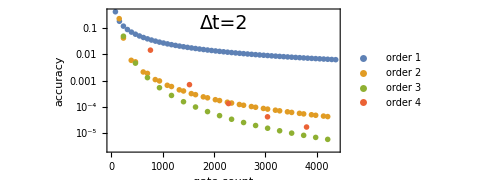

```mathematica
t=2;
deltatwo=ListLogPlot[Table[Transpose@{Total[#]&/@trotsum[t][order]⟦All,1⟧,trotsumsub[t][order]⟦All,2⟧},{order,{1,"2scb",3,4}}],
AspectRatio->1/2,ImageSize->Medium,Epilog->Text[Style["Δt="<>ToString[t],19,FontFamily->"FreeSerif"],Scaled[{.5,.9}]],PlotMarkers->"OpenMarkers",
LabelStyle->{FontFamily->"FreeSerif",FontSize->15,Background->None},FrameLabel->{"gate count","accuracy"},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotStyle->PointSize[Large],Background->White,PlotLegends->Placed[PointLegend[Automatic,( "order "<>ToString[#]&/@Range[4]),Spacings->0,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.1,0.19}],PlotRange->All]
```

```mathematica
Export["/home/cica/chemistry/img/trotter_gates_dists.pdf",deltatwo]
```

/home/cica/chemistry/img/trotter_gates_dists.pdf

```mathematica
rainbowcol[n_]:=Table[ColorData["Rainbow",(i-1)/n],{i,n}]
```

```mathematica
Options@PointLegend
```

{Joined→False,LabelStyle→Automatic,LegendFunction→Identity,LegendLabel→None,LegendLayout→Automatic,LegendMargins→Automatic,LegendMarkers→None,LegendMarkerSize→Automatic,Method→None}

```mathematica
trotallfull=ListLogPlot[
Table[
Flatten[Table[Transpose@{Total[#]&/@trotsum[t][order]⟦All,1⟧,trotsumsub[t][order]⟦All,2⟧},{order,{1,"2scb",3,4}}],1]
,{t,times}],
AspectRatio->5/4,ImageSize->750,PlotMarkers->Automatic,
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},FrameLabel->{"gate count","fullspace distance"},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotStyle->Reverse@rainbowcol[Length@times],Background->White,PlotLegends->Placed[PointLegend[Automatic,( "Δt="<>ToString[#]&/@times),Spacings->0,LegendLayout->"Row",LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.7,0.92}],PlotRange->All,PlotTheme->"Detailed"];
```

```mathematica
trotallsub=ListLogPlot[
Table[
Flatten[Table[Transpose@{Total[#]&/@trotsumsub[t][order]⟦All,1⟧,trotsumsub[t][order]⟦All,2⟧},{order,{1,"2scb",3,4}}],1]
,{t,times}],
AspectRatio->5/4,ImageSize->750,PlotMarkers->Automatic,
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},FrameLabel->{"gate count","subspace distance"},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotStyle->Reverse@rainbowcol[Length@times],Background->White,PlotLegends->Placed[PointLegend[Automatic,( "Δt="<>ToString[#]&/@times),Spacings->0,LegendLayout->"Row",LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.7,0.92}],PlotRange->All,PlotTheme->"Detailed"];
```

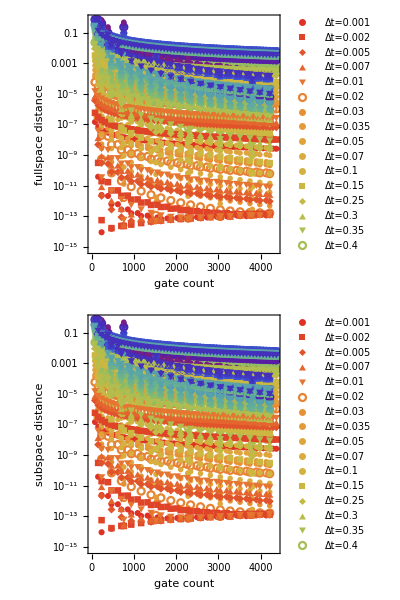

```mathematica
trotall=Column[{trotallfull,trotallsub},Spacings->-.1]
```

```mathematica
Export["/home/cica/chemistry/img/trotter_all.pdf",trotall]
```

/home/cica/chemistry/img/trotter_all.pdf

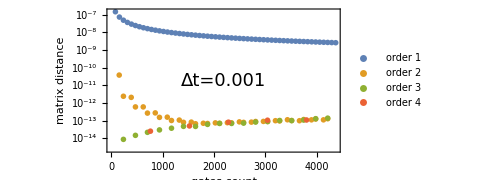
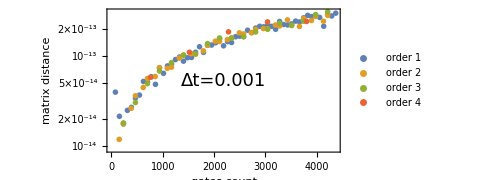
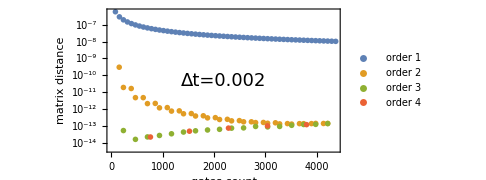
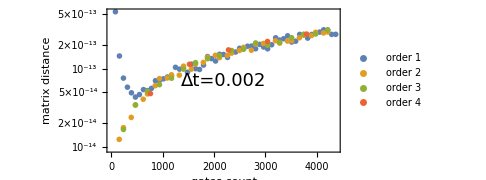
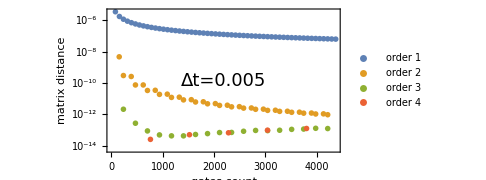
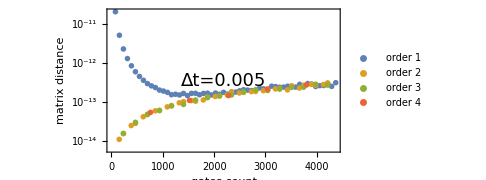
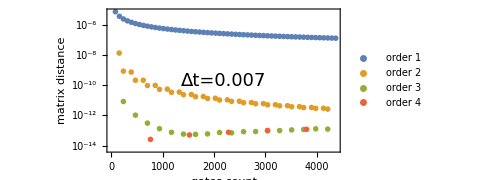
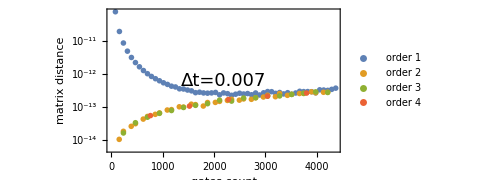

```mathematica
Table[
Row@{ListLogPlot[Table[Transpose@{Total[#]&/@trotsumsub[t][order]⟦All,1⟧,trotsumsub[t][order]⟦All,2⟧},{order,{1,"2scb",3,4}}],opts[t]],
ListLogPlot[Table[Transpose@{Total[#]&/@trotsum[t][order]⟦All,1⟧,trotsumsub[t][order]⟦All,4⟧},{order,{1,"2scb",3,4}}],opts[t]]
}
,{t,times}]
```